Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

```mathematica
Clear["Global`*"]
```

Conformal mapping w=ⅇ^z

1.  Find the image of x = c = const, -π < y ≤ π , under w = ⅇ^z

Three cyan cells with related but not strictly necessary contents. Example 4 on p. 740 covers the conformal mapping under ⅇ^z. A rectangle in the z-plane is mapped to a circular sector in the w-plane. But in the example there are two x-values, as shown in the first plot below, labeled z-plane. Here it is apparent that the radial values mapped by the Exp function vary between 0 and 1, and the angular values vary between 0.5 and 1, and these ranges are reflected in the w-plane map, shown in the second plot. However, Example 4 describes the mapped result as a w-plane circle with radius ⅇ^c, and the text answer to the problem repeats this.

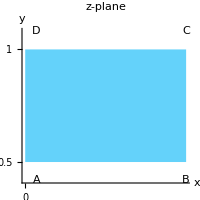
-Graphics--Graphics-

```mathematica
Row[{Graphics[{{{RGBColor[100/255,210/255,250/255],Rectangle[{0,0.5},{1,1}]}},{Text["A",{0.07,0.42}]},{Text["B",{1,0.42}]},{Text["C",{1,1.08}]},{Text["D",{0.07,1.08}]},{}},Axes->True, AxesOrigin->{0,0},PlotRange->{{1.5,-1},{0,1.5}},Ticks->{{0,1,2},{0,0.5,1,1.5}},ImageSize->200,AxesLabel->{"x","y"},PlotLabel->Style[Framed[  "  z-plane "],10,Blue,Background->White]] ,Graphics[{{{RGBColor[100/255,210/255,250/255],Annulus[{0,0},{1,ⅇ},{0.5,1}]}},{Circle[{0,0},1,{0,π}]},{Circle[{0,0},ⅇ,{0,π}]},{Dashed,Line[{{0,0},{3,1.65}}]},{Dashed,Line[{{0,0},{1.85,2.9}}]},{Text["A*",{0.8,0.42}]},{Text["B*",{2.5,1.3}]},{Text["C*",{1.5,2.4}]},{Text["D*",{0.5,0.77}]},{Text["ϕ = 0.5",{3,1.8}]},{Text["ϕ = 1.0",{2.3,2.75}]}},Axes->True, AxesOrigin->{0,0},PlotRange->{{-3,3.5},{-0.5,3}},Ticks->{{-3,-2,-1,0,1,2,3},{0,1,2,3}},ImageSize->280,AxesLabel->{"u","v"},PlotLabel->Style[Framed[  "  w-plane "],10,Red,Background->White]] }]
```

In the present problem only a single constant x-value is called for.  For purposes of illustration, I assume that the constant x-value is Log[2]. Then the two plots shown below are representative of the environment described in the problem. I made sure the z-plane line was “long enough”, although the t values in the second plot are set independently. I see that even though the constant z-plane line is 2π in length, it is only half the length of the w-plane circumference. A little experimentation shows that the w-plane circle “starts” at -2+0 ⅈ.

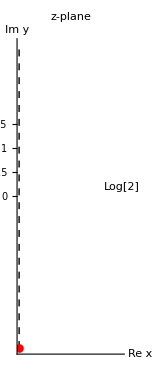
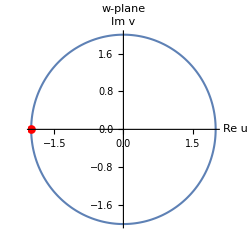

```mathematica
Row[{Graphics[{{Dashed,Line[{{Log[2],-π},{Log[2],π}}]},{Text["Log[2]",{0.95,0.2}]},{Red,PointSize[0.04],Point[{Log[2],-π}]}},Axes->True, AxesOrigin->{0,0},PlotRange->{{1.1,-1},{-3.5,3.5}},Ticks->{{0,1,2},{0,0.5,1,1.5}},ImageSize->155,AxesLabel->{"Re x","Im y"},PlotLabel->Style[Framed[  "  z-plane "],10,Blue,Background->White]],ParametricPlot[{Re[Exp[Log[2]] ⅇ^(ⅈ t)],Im[Exp[Log[2]] ⅇ^(ⅈ t)]},{t,-π,π},ImageSize->250,PlotStyle->{Thickness[0.006]},AxesLabel->{"Re u","Im v"},PlotLabel->Style[Framed[  "  w-plane "],10,Red,Background->White],Epilog->{{Red,PointSize[0.025],Point[{-2,0}]}}]}]
```

The above plot matches the description in the text answer.

3 - 7 Find and sketch the image of the given region under w = ⅇ^z.

3.  -1/2≤x≤1/2, -π≤y≤π

```mathematica
Clear["Global`*"]
```

I didn’t look ahead to notice that this section has a sector-mapping conformation as well as a line-mapping conformation. Anyway, here is the sector conformation again, with transfer points as per the problem description. Notice that the A→B→C→D traverse in w is CCW, not CW as it may appear.

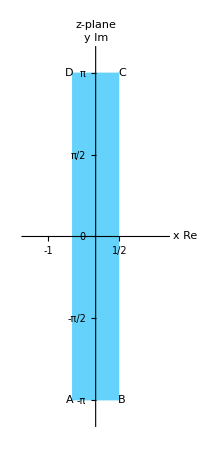
-Graphics--Graphics-

```mathematica
Row[{Graphics[{{{RGBColor[100/255,210/255,250/255],Rectangle[{-1/2,-π},{1/2,π}]}},{Text["A",{-0.55,-π}]},{Text["B",{0.56,-π}]},{Text["C",{0.56,π}]},{Text["D",{-0.56,π}]},{}},Axes->True, AxesOrigin->{0,0},PlotRange->{{-1.5,1.5},{-3.5,3.5}},Ticks->{{-1,-1/2,0,1/2,1},{-π,-π/2,0,π/2,π}},ImageSize->200,AxesLabel->{"x Re","y Im"},PlotLabel->Style[Framed[  "  z-plane "],10,Blue,Background->White]] ,Graphics[{{{RGBColor[100/255,210/255,250/255],Annulus[{0,0},{ⅇ^(-.5),ⅇ^(.5)},{-π,π}]}},{Dashed,Line[{{0,0},{-3,0}}]},{Text["A*",{-0.5,-0.15}]},{Text["B*",{-1.7,-0.15}]},{Text["C*",{-1.7,0.15}]},{Text["D*",{-0.5,0.15}]},{Text["ϕ=-π=π",{-3,0.15}]}},Axes->True, AxesOrigin->{0,0},PlotRange->{{-3.5,3.5},{-3.5,3.5}},Ticks->{{-3,-2,-1,0,1,2,3},{0,1,2,3}},ImageSize->280,AxesLabel->{"u","v"},PlotLabel->Style[Framed[  "  w-plane "],10,Red,Background->White]] }]
```

The above plot matches the text answer.

5.  - ∞ < x < ∞, 0 <= y <= 2 π

```mathematica
Clear["Global`*"]
```

The plot shown below comes from Weisstein’s MathWorld, a different format than I have used up to now. There is one thing about this, which is that x cannot take on the value of -∞, because it isn’t included in Exp’s domain.  I believe Mathematica has adapted its plot to show off the pole. The left plot shows the mapping process by use of toy values of x, while the right plot is the real deal.

```mathematica
d1=ImplicitRegion[-∞<x<∞∧-π≤y≤π,{x,y}];
```

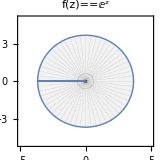
-Graphics--Graphics-

```mathematica
Row[{ParametricPlot[Through[{Re,Im}[Exp[x+ⅈ y]]],{x,-100,1.3},{y,-π,π}, PlotRange->{{-5,5},{-5,5}},PlotLabel->f[z]==Exp[z],ImageSize->160,PlotStyle->{Thick,Opacity[0.05],Black},Frame->True,Axes->False],ParametricPlot[Through[{Re,Im}[Exp[x+ⅈ y]]],{x,y}∈d1, PlotRange->{{-5,5},{-5,5}},PlotLabel->f[z]==Exp[z],ImageSize->160,PlotStyle->{Thick,Opacity[0.05],Black},Frame->True,Axes->False]}]
```

The right plot above matches the description of the text answer.

7.  0 <x <1, 0 < y < π

Another example of a sector-mapping task. In this problem the CCW traverse of the mapped sector is clear.

```mathematica
Clear["Global`*"]
```

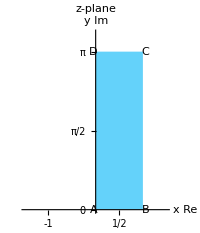
-Graphics--Graphics-

```mathematica
Row[{Graphics[{{{RGBColor[100/255,210/255,250/255],Rectangle[{0,0},{1,π}]}},{Text["A",{-0.05,0}]},{Text["B",{1.06,0}]},{Text["C",{1.06,π}]},{Text["D",{-0.06,π}]},{}},Axes->True, AxesOrigin->{0,0},PlotRange->{{-1.5,1.5},{0,3.5}},Ticks->{{-1,-1/2,0,1/2,1},{-π,-π/2,0,π/2,π}},ImageSize->200,AxesLabel->{"x Re","y Im"},PlotLabel->Style[Framed[  "  z-plane "],10,Blue,Background->White]] ,Graphics[{{{RGBColor[100/255,210/255,250/255],Annulus[{0,0},{ⅇ^0,ⅇ^1},{0,π}]}},{Dashed,Line[{{-3,0},{3,0}}]},{Text["A*",{0.9,-0.1}]},{Text["B*",{2.9,-0.1}]},{Text["C*",{-2.6,-0.15}]},{Text["D*",{-01,-0.15}]},{Text["ϕ=-π",{-3,0.15}]},{Text["ϕ=π",{3,0.15}]}},Axes->True, AxesOrigin->{0,0},PlotRange->{{-3.5,3.5},{0,3.5}},Ticks->{{-3,-2,-1,0,1,2,3},{0,1,2,3}},ImageSize->280,AxesLabel->{"u","v"},PlotLabel->Style[Framed[  "  w-plane "],10,Red,Background->White]] }]
```

The above plot matches the description of the text answer.

Conformal mapping w=Sin[z]

9.  Find the points at which w = Sin[z] is not conformal.

The discussion of the sine function on p. 751 makes clear that sin x is not conformal at ±2 π, also stating that the vertical strip S: -1/2 π≤ x ≤ 1/2 π is used for figure 391. The implication is that a strip of π width domain is the normal practice with this function. For this reason it is unclear why the answer gives ±(2 n+1)π/2 as the points where Sin[z] in not conformal. I assume it means that I have a choice of which strip to use, (though only one), depending on the details of the problem at hand.

11 - 14 Find and sketch or graph the image of the given region under w = Sin[x]

11.  0<x<π/2, 0 ,<y<2

```mathematica
Clear["Global`*"]
```

The mapping function referred to as sine transformation has the details

w == u + ⅈ v == Sin[z] == Sin[x] Cosh[y] + ⅈ Cos[x] Sinh[y]

What if I just blindly plug this into a plot? Seems to work. The path of action can be seen in the congruence of point colors. (To place the points on the middle plot, I broke up the sine formula into prearranged pieces.)

The third plot is a plot of the text answer, which matches the w-plane solution.

```mathematica
d1=ImplicitRegion[0<x<π/2∧0<y<2,{x,y}];
```

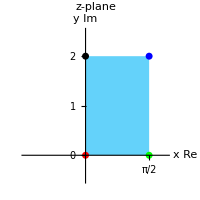
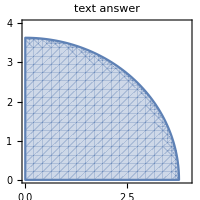
-Graphics--Graphics--Graphics-

```mathematica
Row[{Graphics[{{{RGBColor[100/255,210/255,250/255],Rectangle[{0,0},{π/2,2}]}},{Black,PointSize[0.025],Point[{0,2}]},{Red,PointSize[0.025],Point[{0,0}]},{Green,PointSize[0.025],Point[{π/2,0}]},{Blue,PointSize[0.025],Point[{π/2,2}]}},Axes->True, AxesOrigin->{0,0},PlotRange->{{-1.5,2},{-0.5,2.5}},Ticks->{{-π/2,0,π/2},{0,1,2}},ImageSize->200,AxesLabel->{"x Re","y Im"},PlotLabel->Style[Framed[  "  z-plane "],10,Blue,Background->White]],ParametricPlot[{Re[Sin[x] Cosh[y]+ⅈ Cos[x] Sinh[y]],Im[Sin[x] Cosh[y]+ⅈ Cos[x] Sinh[y]]},{x,y}∈d1,ImageSize->250,PlotStyle->{RGBColor[100/255,210/255,250/255],Opacity[1.0],Thickness[0.006]},AxesLabel->{"Re u","Im v"},PlotLabel->Style[Framed[  "  w-plane "],10,Red,Background->White],PlotRange->{{-1/2,4.5},{-1/2,4.5}},Epilog->{{Red,PointSize[0.025],Point[{Sin[x] Cosh[y]/.{x->0,y->0}, Cos[x] Sinh[y]/.{x->0,y->0}}]},{Green,PointSize[0.025],Point[{Sin[x] Cosh[y]/.{x->π/2,y->0}, Cos[x] Sinh[y]/.{x->π/2,y->0}}]},{Blue,PointSize[0.025],Point[{Sin[x] Cosh[y]/.{x->π/2,y->2}, Cos[x] Sinh[y]/.{x->π/2,y->2}}]},{Black,PointSize[0.025],Point[{Sin[x] Cosh[y]/.{x->0,y->2}, Cos[x] Sinh[y]/.{x->0,y->2}}]}}],RegionPlot[u^2/Cosh[2]^2+v^2/Sinh[2]^2<1,{u,0,4},{v,0,4},ImageSize->200,PlotLabel->Style[Framed[  " text answer "],10,Green,Background->White]]}]
```

13.  0 < x < 2 π, 1 < y < 3

```mathematica
Clear["Global`*"]
```

Here is another problem, which looks very similar to the last. Regarding the superposition of points in the middle plot: it looks like either red/black or green/brown have to define the line of origin. Whichever case it is, the z-plane domain either has to rotate clockwise (which I thought was a negative sense) or else rotate “through the paper” before beginning a ccw rotation.

```mathematica
d1=ImplicitRegion[0<x<2π∧1<y<3,{x,y}];
```

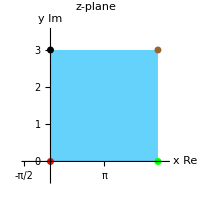
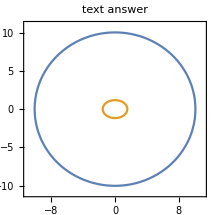
-Graphics--Graphics--Graphics-

```mathematica
Row[{Graphics[{{{RGBColor[100/255,210/255,250/255],Rectangle[{0,0},{2π,3}]}},{Black,PointSize[0.025],Point[{0,3}]},{Red,PointSize[0.025],Point[{0,0}]},{Green,PointSize[0.025],Point[{2π,0}]},{Brown,PointSize[0.025],Point[{2π,3}]}},Axes->True, AxesOrigin->{0,0},PlotRange->{{-1.5,2π+0.5},{-0.5,3.5}},Ticks->{{-π/2,0,π/2,π,(3π)/2,2π},{0,1,2,3}},ImageSize->200,AxesLabel->{"x Re","y Im"},PlotLabel->Style[Framed[  "  z-plane "],10,Blue,Background->White]],ParametricPlot[{Re[Sin[x] Cosh[y]+ⅈ Cos[x] Sinh[y]],Im[Sin[x] Cosh[y]+ⅈ Cos[x] Sinh[y]]},{x,y}∈d1,ImageSize->250,PlotStyle->{RGBColor[100/255,210/255,250/255],Opacity[1.0],Thickness[0.006]},AxesLabel->{"Re u","Im v"},PlotLabel->Style[Framed[  "  w-plane "],10,Red,Background->White],Epilog->{{Red,PointSize[0.06],Point[{Sin[x] Cosh[y]/.{x->0,y->0}, Cos[x] Sinh[y]/.{x->0,y->0}}]},{Green,PointSize[0.025],Point[{Sin[x] Cosh[y]/.{x->2π,y->0}, Cos[x] Sinh[y]/.{x->2π,y->0}}]},{Black,PointSize[0.06],Point[{Sin[x] Cosh[y]/.{x->0,y->3}, Cos[x] Sinh[y]/.{x->0,y->3}}]},{Brown,PointSize[0.025],Point[{Sin[x] Cosh[y]/.{x->2π,y->3}, Cos[x] Sinh[y]/.{x->2π,y->3}}]}}],ContourPlot[{u^2/Cosh[3]^2+v^2/Sinh[3]^2==1,u^2/Cosh[1]^2+v^2/Sinh[1]^2==1},{u,-11,11},{v,-11,11},ImageSize->215,PlotLabel->Style[Framed[  " text answer "],10,Green,Background->White],Axes->True]}]
```

15.  Describe the mapping w = Cosh[z] in terms of the mapping w = Sin[z] and rotations and translations.

On p. 752 the Cosh mapping is described, w = Cosh[z] = Cos[ⅈ z]. A two-step mapping, first z→Z (a rotation),then Z→w, consisting of the mapping w = Cos[Z]. I didn’t see anything relative to Sin[z], though it may relate to assessing conformity, with the derivative.

17.  Find an analytic function that maps the region R bounded by the positive x- and y-semi-axes and the hyperbola x y = π in the first quadrant onto the upper half-plane. Hint. First map R onto a horizontal strip.

```mathematica
Clear["Global`*"]
```

The region in question is shown below. At http://mathfaculty.fullerton.edu/mathews/c2003/ComplexFunPowerRootMod.html it is shown that a square root function can be used to map a horizontal line onto a hyperbolic curve. This is presented as a two-way development, so that the inverse of the mapping function can disassemble the hyperbola into a line. Except that I am asked to deal with regions rather than lines. The first plot (left) shows the problem conditions. The (right) plot shows the square root function with the necessary parameter values to duplicate the region plot. Note that points on the two plots are equivalent, e.g. {1+π ⅈ} and {2+π/2 ⅈ}. The y-interval in the parametric plot seems important in obtaining the desired output; for example, if y only goes to π instead of to 2π, the correct hyperbola is not generated.

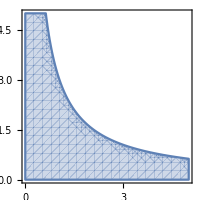
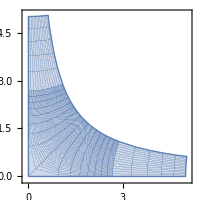

```mathematica
Row[{RegionPlot[{0<x&&0<y&&x y<π},{x,0,5},{y,0,5},ImageSize->200],ParametricPlot[Through[{Re,Im}[(x+ⅈ y)^(1/2)]],{x,-25,25},{y,0,2π}, PlotRange->{{-0.1,5.1},{-0.1,5.1}},Frame->True,ImageSize->200]}]
```

Now come the mappings. In the first plot below (left), I follow the process in the web page I cited. Using the domain chosen for x and y, the parametric plot of square root maps to a hyperbola. Inversely, squaring and preserving the domain and range unchanged from the previous parametric plot, brings it back to a strip. I am also referencing a related web page, namely https://www.patrickstevens.co.uk/useful-conformal-mappings/, which suggests using Exp function to map to a half plane. The plot utilizing this approach is shown below center and right. The increasing Arg quantities of the center and right plots show how the function engulfs the upper half plane, with a final y-interval 0 to 2π, as set originally. The mapping transform itself was altered by setting the Arg to y/2 instead of y, in order to restrict the mapping to the upper half instead of the entire plane.

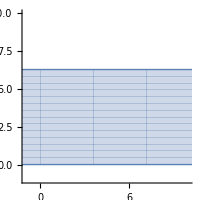
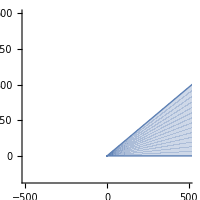
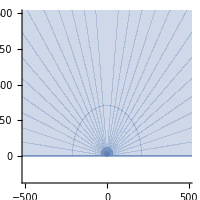

```mathematica
Row[{ParametricPlot[Through[{Re,Im}[(√(x+ⅈ y))^2]],{x,-25,25},{y,0,2π}, PlotRange->{{-1,10},{-1,10}},Frame->False,ImageSize->200],ParametricPlot[Through[{Re,Im}[Exp[x+ⅈ y/12]]],{x,-25,25},{y,0,2π}, PlotRange->{{-500,500},{-100,600}},Frame->False,ImageSize->200],
ParametricPlot[Through[{Re,Im}[Exp[x+ⅈ y/2]]],{x,-25,25},{y,0,2π}, PlotRange->{{-500,500},{-100,600}},Frame->False,ImageSize->200]}]
```

It is obvious this does not agree with the text answer. Just for form’s sake I run

```mathematica
PossibleZeroQ[ⅇ^((x+ⅈ y)/2)-ⅇ^((x+ⅈ y)^2/2)]
```

False

When I try out the text answer I get

```mathematica
ParametricPlot[Through[{Re,Im}[Exp[(x+ⅈ y)^2/2]]],{x,-25,25},{y,0,2 π}, PlotRange->{{-500,500},{-100,600}},Frame->False,ImageSize->200]
```

-Graphics-

Which is saturated not twice but more (four times?) with points, as well as covering the entire plane. The best I could do at single saturation was to run y from 0 to about 0.88, but it is not uniform in coverage.

Conformal mapping x = Cos[z]

19. Find the images of the lines x = c = const under the mapping w = Cos[z].

```mathematica
Clear["Global`*"]
```

The text covers application of the cosine function on pg 750-752, treating it as an offshoot of the sine function. Ellipses and hyperbolas are mentioned, but what is not clear is that when it comes to mapping vertical lines from the z-plane, the hyperbola will be the w-plane result, and when horizontal lines are mapped, the mapping is to ellipses. A useful and straightforward explanation and worksheet is at https : // sites.oxy.edu/ron/math/312/14/projects/Richardson.pdf, and I used it for the below. The point a will be the const point from the x-axis.

The four cells below reflect the answer in the text.

Showing the mappings of five random vertical lines.

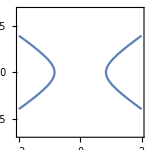
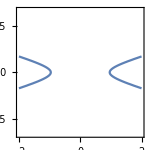
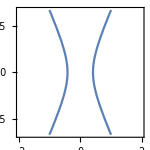
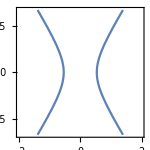
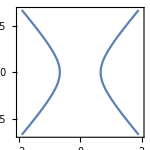

```mathematica
Row[Table[ContourPlot[u^2/Cos[a]^2- v^2/Sin[a]^2==1,{u,-2,2},{v,-2,2},ImageSize->150],{a,{-10,-6,-2,1,2.3}}]]
```

Showing below the attempted mapping of three troublesome vertical lines. It looks like all three hit the singularity target.

```mathematica
Row[Table[ContourPlot[u^2/Cos[a]^2- v^2/Sin[a]^2==1,{u,-2,2},{v,-2,2},ImageSize->150],{a,{-π,0,π}}]];
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

20 - 23 Find and sketch or graph the image of the given region under the mapping w = Cos[z].

21.  0<x<π/2, 0<y<2 directly and from problem 11

```mathematica
Clear["Global`*"]
```

The instructions are a little tricky. What does “from problem 11” mean? The text does not cover Cosine mapping directly, allowing only two lines of text to say to add π/2 to z and use the Sine function. That’s as “direct” as its coverage is. So I took the easy way and followed the text’s advice. Note that the ImplicitRegion in yellow has been bumped up, and does not match the problem. So although in the first graphic the z-plane rectangle is the proper one, in the middle plot the point location substitutions have been altered to reflect the nudge. Because the middle plot uses d1, and d1 has the nudge, I believe the sequence of point colors is correct. (Aside: I find that I can’t trim the PlotRange in the center plot to reduce upper y (or v) to less than 2 without distorting the plot. I don’t understand why.)

```mathematica
d1=ImplicitRegion[π/2<x<π∧0<y<2,{x,y}];
```

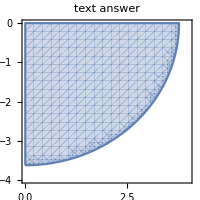
-Graphics--Graphics--Graphics-

```mathematica
Row[{Graphics[{{{RGBColor[100/255,210/255,250/255],Rectangle[{0,0},{π/2,2}]}},{Black,PointSize[0.025],Point[{0,2}]},{Red,PointSize[0.025],Point[{0,0}]},{Green,PointSize[0.025],Point[{π/2,0}]},{Blue,PointSize[0.025],Point[{π/2,2}]}},Axes->True, AxesOrigin->{0,0},PlotRange->{{-1.5,2},{-0.5,2.5}},Ticks->{{-π/2,0,π/2},{0,1,2}},ImageSize->200,AxesLabel->{"x Re","y Im"},PlotLabel->Style[Framed[  "  z-plane "],10,Blue,Background->White]],ParametricPlot[{Re[Sin[x] Cosh[y]+ⅈ Cos[x] Sinh[y]],Im[Sin[x] Cosh[y]+ⅈ Cos[x] Sinh[y]]},{x,y}∈d1,ImageSize->250,PlotStyle->{RGBColor[100/255,210/255,250/255],Opacity[1.0],Thickness[0.006]},AxesLabel->{"Re u","Im v"},PlotLabel->Style[Framed[  "  w-plane "],10,Red,Background->White],PlotRange->{{-1/2,4.5},{-4,2}},Epilog->{{Red,PointSize[0.025],Point[{Sin[x] Cosh[y]/.{x->π/2,y->0}, Cos[x] Sinh[y]/.{x->π/2,y->0}}]},{Green,PointSize[0.025],Point[{Sin[x] Cosh[y]/.{x->π,y->0}, Cos[x] Sinh[y]/.{x->π,y->0}}]},{Blue,PointSize[0.025],Point[{Sin[x] Cosh[y]/.{x->π,y->2}, Cos[x] Sinh[y]/.{x->π,y->2}}]},{Black,PointSize[0.025],Point[{Sin[x] Cosh[y]/.{x->π/2,y->2}, Cos[x] Sinh[y]/.{x->π/2,y->2}}]}}],RegionPlot[u^2/Cosh[2]^2+v^2/Sinh[2]^2<1,{u,0,4},{v,-4,0},ImageSize->200,PlotLabel->Style[Framed[  " text answer "],10,Green,Background->White]]}]
```

23.  π < x < 2 π, y < 0

```mathematica
Clear["Global`*"]
```

```mathematica
N[250/255]
```

0.980392

What to do with this one? It seems the most reasonable approach is to use the same nudge trick as in the last problem. An urge to convey infinite vertical depth below the horizontal axis. This is easy for the Graphic but a puzzler for the function plot. Sort of a groaner for now, but maybe I will just tack on a polygon to the plot range in the plot on the right. (Arbitrarily ignoring the horizontal infinitude.)

```mathematica
kru=RGBColor[0.392,0.823,0.98];
```

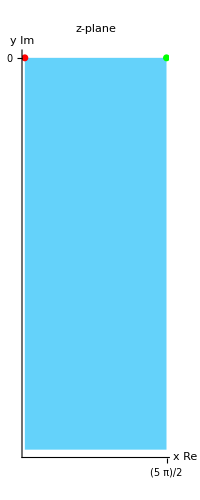
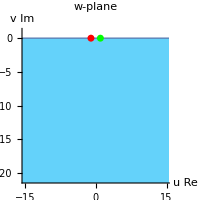

```mathematica
Row[{Graphics[{{kru,Polygon[{{(3π)/2,0},{(3π)/2,-11},{(5π)/2,-11},{(5π)/2,0}},VertexColors->{kru,White,White,kru}]},{Red,PointSize[0.025],Point[{(3π)/2,0}]},{Green,PointSize[0.025],Point[{(5π)/2,0}]}},Axes->True, AxesOrigin->{0,0},PlotRange->{{-1.5,10},{0.5,-10}},Ticks->{{0,(3π)/2,(5π)/2},{0,1,2}},ImageSize->200,AxesLabel->{"x Re","y Im"},PlotLabel->Style[Framed[  "  z-plane "],10,Blue,Background->White]],ParametricPlot[Through[{Re,Im}[Sin[x] Cosh[y]+ⅈ Cos[x] Sinh[y]]],{x,(3π)/2,(5π)/2},{y,-6,0}, PlotRange->{{-15,15},{-21,1}},Frame->False,PlotStyle->{Opacity[1.0],kru},Epilog->{{Red,PointSize[0.025],Point[{Sin[x] Cosh[y]/.{x->(3π)/2,y->0}, Cos[x] Sinh[y]/.{x->(3π)/2,y->0}}]},{Green,PointSize[0.025],Point[{Sin[x] Cosh[y]/.{x->(5π)/2,y->0}, Cos[x] Sinh[y]/.{x->(5π)/2,y->0}}]},{kru,Polygon[{{-15,-10},{-15,-21},{15,-21},{15,-10}},VertexColors->{kru,White,White,kru}]}},AxesLabel->{"u Re","v Im"},ImageSize->200,PlotLabel->Style[Framed[  "  w-plane "],10,Red,Background->White]]}]
```

The w-plane plot above matches the descriptive answer in the text.